# Projekt 3 Rapport

Kurskod: IX1501
Datum: 2018-10-09

Evan Saboo, saboo@kth.se

Uppgift 1: Simulation of Profit

## Sammanfattning & Uträkning

### Uppgift

I ett café produceras och säljs kakor. Kakorna säljs till kunder för €p under dagen och de resterande säljs till en restaurang för €s per kaka.
Nedan ges mer information om caféts försäljning :

c - cost of production, c∈N(8,2) €

p - sales price, p=€18

s - scrap value (priset restaurangen betalar) s=⌊x⌋,x∈N(5,1)€

ℓ - cost of cake shortage (per kaka) ℓ=0

n - demand of cakes during a day (antalet kakor) n∈Po(12)

q - quantity (antalet producerade kakor)

P - profit (under en dag)

I denna uppgift utfördes nedanstående deluppgifterna:

Bestäm en formel för vinsten. Observera att det finns två olika fall:  n≤q och n>q.

Simulera ett lämpligt antal arbetsdagar och skapa 95% konfidensintervaller (längd < €10) för den genomsnittliga vinsten vid 5≤q≤20.

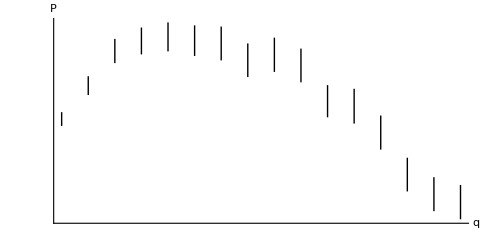
Rita konfidensintervallerna i ett diagram som liknar följande:

-Graphics-

Vad är det mest lönsamma antalet kakor att producera?

### Resultat

#### Formel för vinsten

Med de nedan angivna parametrar fick jag ut en formel som var uppdelat i två delar, en för n≤q och en annan för n>q.

c - cost of production, c∈N(8,2) €
p - sales price, p=€18
s - scrap value, s=⌊x⌋,x∈N(5,1)€
n - demand, n∈Po(12)
q - quantity
P - profit

n≤q <->P(q) =  p*n+(q-n)*s-q*c   
 n>q <->P(q) =  p*q-q*c

#### Konfidensintervall för genomsnittlig vinst

För att få ut konfidensintervaller för genomsnittlig vinst P(q) för alla q där 5≤q≤20 använder man formeln:

ci_μ≈x̄±Q_𝔱(n-1,(1+c)/2)s/(√n)
n= 1000 dagar
Q_𝔱 = kvantil av StudentT fördelning 
 x̄ = uppskattning av medelvärdet för varje q 
c = 0.95
s = uppskattning av standardavvikelsen för varje

Med folmen fick blev intervallerna:

q=5 → 49.2809≤P(5)≤50.5109 
q=6 → 58.5198≤P(6)≤60.0267
q=7 → 67.9932≤P(7)≤69.8190
q=8 → 76.0464≤P(8)≤78.4503
q=9 → 84.5777≤P(9)≤87.3486
q=10 → 91.7616≤P(10)≤94.891 
q=11 → 95.4021≤P(11)≤99.2954
q=12 → 99.5713≤P(12)≤103.7971 
q=13 → 99.4513≤P(13)≤104.5051 
q=14 → 100.6190≤P(14)≤106.0117 
q=15 → 101.9353≤P(15)≤107.9960 
q=16 → 98.9419≤P(16)≤105.3715 
q=17 → 98.5622≤P(17)≤105.4853
q=18 → 93.0272≤P(18)≤100.0994 
q=19 → 91.2772≤P(19)≤98.7452 
q=20 → 86.2523≤P(20)≤ 93.6167

#### Diagram över konfidensintervallen

Med hjälp av den inbygga funktionen  ListLinePlot kunde jag plotta alla 16 intervallerna i en graf:

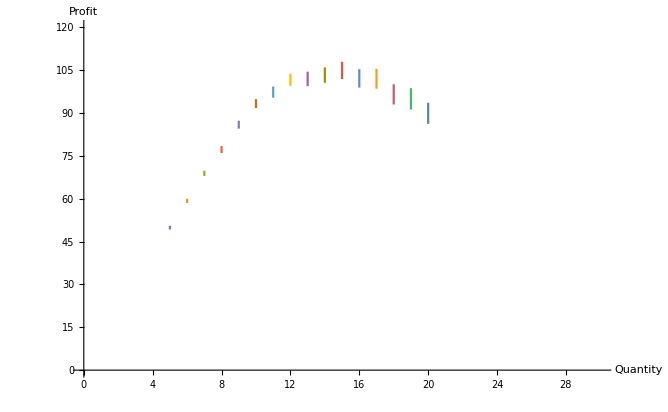

#### Mest lönsamma antalet kakor att producera

I den förgående deluppgiften kan man redan se att man behöver bara producera mellan 14-15 kakor för att gå mest i vinst.
Jag skapade också en metod som tar ut medelvärdet av alla q där 5≤q≤20 och kollade vilken q som fick mest i vinst. Detta gjordes 1000 gånger för att få ut en frekvens av alla q som vann för att kolla den som hade störta frekvensen:

q = 14 → frekvens=420  
 q = 15 → frekvens=310  
 q = 16 → frekvens=70  
 q = 17 → frekvens=11

Man kan se ovan att  q = 15 & q = 14 är dee mest lönsamma antalet kakor man behöver producera.

## Kod

```mathematica
ClearAll["`*"]
```

#### Formula for the profit

```mathematica
costDist = NormalDistribution[8,2];
scrapDist = NormalDistribution[5, 1];
demandDist = PoissonDistribution[12];
```

```mathematica
cakePrice = 18;
```

```mathematica
(* When n ≤ q *)
p[{quantity_, prodcost_, demand_}/; demand≤ quantity] := cakePrice*demand +(quantity - demand)*Floor[RandomVariate[scrapDist,1][[1]]] - quantity* prodcost;
```

```mathematica
(* When n > q *)
p[{quantity_, prodcost_, demand_}/; demand > quantity] := cakePrice * quantity - quantity* prodcost;

Profit[q_] := p[{q,RandomVariate[costDist, 1][[1]],RandomVariate[demandDist, 1][[1]]}];
```

#### Confidence intervals for average profit

```mathematica
cInterval[quantity_, days_] := 
Module[{profits,quantile, Xbar, S},
profits = Table[Profit[quantity], days];
Xbar = Mean[profits];
S =StandardDeviation[profits]; 
quantile = Quantile[StudentTDistribution[days-1], 0.975];
{Xbar - quantile*(S/Sqrt[days]), Xbar+ quantile*(S/Sqrt[days])}
];
```

```mathematica
wDays = 1000;
```

```mathematica
intervals = Quiet[Table[cInterval[n, wDays], {n, 5, 20}]]
```

{{49.2809,50.5109},{58.5198,60.0268},{67.9932,69.8191},{76.0465,78.4504},{84.5778,87.3487},{91.7616,94.8915},{95.4021,99.2954},{99.5713,103.797},{99.4514,104.505},{100.619,106.012},{101.935,107.996},{98.942,105.372},{98.5622,105.485},{93.0273,100.099},{91.2772,98.7453},{86.2523,93.6167}}

#### Diagram of the confidence intervals

```mathematica
list = {};
i = 5;
While[i ≤ 20,
temp = intervals[[i-4]];
AppendTo[list, {{i, temp[[1]]},{i, temp[[2]]}}];
i++
];
```

```mathematica
list
```

{{{5,49.2809},{5,50.5109}},{{6,58.5198},{6,60.0268}},{{7,67.9932},{7,69.8191}},{{8,76.0465},{8,78.4504}},{{9,84.5778},{9,87.3487}},{{10,91.7616},{10,94.8915}},{{11,95.4021},{11,99.2954}},{{12,99.5713},{12,103.797}},{{13,99.4514},{13,104.505}},{{14,100.619},{14,106.012}},{{15,101.935},{15,107.996}},{{16,98.942},{16,105.372}},{{17,98.5622},{17,105.485}},{{18,93.0273},{18,100.099}},{{19,91.2772},{19,98.7453}},{{20,86.2523},{20,93.6167}}}

```mathematica
ListLinePlot[list, PlotRange->{{0,30},{0,120}}, AxesLabel->{"Quantity","Profit"}]
```

-Graphics-

#### Most profitable number of cakes to produce

```mathematica
qProfit[days_] := 
Module[{profits,quantile, Xbar, S, i, q=5, prevX = -1000},
For[i = 5, i ≤ 20, i++, 
profits = Table[Profit[i], days];
Xbar = Mean[profits];
If[Xbar > prevX, q = i ; prevX = Xbar, 0];
];
q
];
```

```mathematica
Tally[Table[ qProfit[1000], 1000]]
```

{{14,420},{15,310},{13,187},{16,70},{17,11},{12,1},{18,1}}